# Gametic Selection, Sex Ratio Bias, and Transitions Between Sex Determination Systems

## Michael Scott, Matthew Osmond, Sarah Otto

# A. Offspring control (neo-Y, neo-W, or ESD invade XY)

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_]->r/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_]->(1-r)R/2
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->(1-α)pXm,
Subscript[fHap, X,a,M,male]->(1-α)(1-pXm),
Subscript[fHap, Y,A,M,male]->α pYm,
Subscript[fHap, Y,a,M,male]->α(1-pYm),
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
}/.α->1/2;
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male]
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1,
Subscript[wHap, a,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wDip, A,A,sex_]->1,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1+ Subscript[sDip, sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1-2 pA sDip_female+4 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female-pA sHap_female+pA^2 sHap_female-pA sHap_male+pA^2 sHap_male),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA sHap_female+pA^2 sHap_female+pA r sHap_female-pA^2 r sHap_female-pA r sHap_male+pA^2 r sHap_male),1/2 ϵ (pXf1 r-pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA r sHap_female+pA^2 r sHap_female-pA sHap_male+pA^2 sHap_male+pA r sHap_male-pA^2 r sHap_male)}

And we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)}}

## Resident stability (weak selection) [slow, do not need to re-run]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

## Sex chromosome turnover (weak selection) [slow]

Here we are interested in the ability of a rare mutation at the modifier locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection gives

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→(-1+r) (-1+R),λ→1-r-R+2 r R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

And on the 2nd order (this takes a few minutes)

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{-1/2 dpAXmXf k (2 (-1+k) (1-pA+(-1+2 pA) h_female) sDip_female-2 (-1+k) (1-pA+(-1+2 pA) h_male) sDip_male+k (sHap_female-sHap_male))+dpAYmXf (k^2 (-1+pA+(1-2 pA) h_female) sDip_female+(-1+k)^2 (1-pA+(-1+2 pA) h_male) sDip_male-(k^2 sHap_female)/2+sHap_male-2 k sHap_male+(k^2 sHap_male)/2)-1/R(-1+pA) pA (k^2 (1-pA+(-1+2 pA) h_female)^2 sDip_female^2+(-1+k)^2 (-1+pA+(1-2 pA) h_male)^2 sDip_male^2+(-1+k) (1-pA+(-1+2 pA) h_male) sDip_male ((-R+k (-2+3 R)) sHap_female+(-2+k (2-3 R)+R) sHap_male)-k (1-pA+(-1+2 pA) h_female) sDip_female (2 (-1+k) (1-pA+(-1+2 pA) h_male) sDip_male+(-2 k-2 R+3 k R) sHap_female+(-2+2 k+2 R-3 k R) sHap_male)-(k sHap_female-(-1+k) sHap_male) ((-R+k (-1+2 R)) sHap_female+(-1+k+R-2 k R) sHap_male))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.weaksel/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf},Simplify]
```

{-(((-1+h_female) sDip_female+(-1+h_male) sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (sDip_male sHap_female-h_male sDip_male (sDip_female+2 sHap_female)-sDip_female sHap_male+h_female sDip_female (sDip_male+2 sHap_male)) (-k^2 R sDip_female sHap_female+2 k^2 r R sDip_female sHap_female-2 r sDip_male sHap_female+8 k r sDip_male sHap_female-8 k^2 r sDip_male sHap_female+2 R sDip_male sHap_female-4 k R sDip_male sHap_female+3 k^2 R sDip_male sHap_female-8 k r R sDip_male sHap_female+10 k^2 r R sDip_male sHap_female+2 r sDip_female sHap_male-8 k r sDip_female sHap_male+8 k^2 r sDip_female sHap_male-2 R sDip_female sHap_male+4 k R sDip_female sHap_male-3 k^2 R sDip_female sHap_male+8 k r R sDip_female sHap_male-10 k^2 r R sDip_female sHap_male+k^2 R sDip_male sHap_male-2 k^2 r R sDip_male sHap_male-2 h_male sDip_male ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_female+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap_female+k^2 (1-2 r) R sHap_male)+2 h_female sDip_female ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip_male+k^2 (1-2 r) R sHap_female+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap_male)))/(2 r R ((1-2 h_female) sDip_female+(1-2 h_male) sDip_male)^4)}

Under some situations this reduces to (dividing by van Doorn and Kirkpatricks VA>0 and LA>0 when appropriate):

a) dominant feminizer (neo-W) with no competition among eggs and free recombination with VS locus (and equal dominance coefficients)

```mathematica
selFeminizer=Collect[tester/(pA(1-pA))/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.Subscript[sHap, female]->0//Simplify,{Subscript[sHap, male]},FullSimplify]
```

{-(sDip_female ((2 r (-1+R)+R) sDip_female+(-1+2 r) R sDip_male) sHap_male^2)/(2 r R (sDip_female+sDip_male)^2)}

with free recombination between the VS and modifier locus this reduces to

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/.Subscript[sHap, female]->0/.R->1/2//Simplify,{Subscript[sHap, male]},FullSimplify]
```

{(sDip_female (-sDip_female+sDip_male) sHap_male^2)/(2 (sDip_female+sDip_male)^2)}

b) dominant masculinizer (neo-Y) with no competition among eggs  (and equal dominance coefficients)

```mathematica
selMasculinizer=Collect[tester/(pA(1-pA))/.realsol[[3]]/.Subscript[h, sex_]->h/.k->0/.Subscript[sHap, female]->0//Simplify,{sHap[male]},FullSimplify]
```

{((r-R) sDip_female^2 sHap_male^2)/(r R (sDip_female+sDip_male)^2)}

c) perfect ESD (half females, half males) with no competition among eggs (and equal dominance coefficients)

```mathematica
selESDsimp=Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.Subscript[h, sex_]->h/.k->1/2/.Subscript[sHap, female]->0//Simplify,{sHap[female],sHap[male]},Simplify]
```

{-(sDip_female (3 sDip_female-sDip_male) sHap_male^2)/(8 (sDip_female+sDip_male)^2)}

This is an average of masculinizers and feminizers with free recombination between the VS and modifier locus

```mathematica
Factor[1/2*(selFeminizer+selMasculinizer)/2/.R->1/2]
0==%-selESDsimp*(1-2r)/r//Factor
```

{((-1+2 r) sDip_female (3 sDip_female-sDip_male) sHap_male^2)/(8 r (sDip_female+sDip_male)^2)}

0=={0}

Note that R is involved if the ESD is not perfect (k ≠ 1/2)

```mathematica
Collect[tester/(pA(1-pA))/.realsol[[3]]/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0//Simplify,{Subscript[sHap, male]},Simplify]
```

{-(sDip_female (((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sDip_female+k^2 (-1+2 r) R sDip_male) sHap_male^2)/(2 r R (sDip_female+sDip_male)^2)}

## Sex chromosome turnover (selection not assumed to be weak)

### Characteristic polynomial

In this section we do not assume weak selection.

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pYm) Subscript[wHap, a,male] Subscript[wDip, a,a,male]+
pXf Subscript[wHap, A,female] (1-pYm) Subscript[wHap, a,male] Subscript[wDip, A,a,male]+
(1-pXf)Subscript[wHap, a,female] pYm Subscript[wHap, A,male] Subscript[wDip, a,A,male] +
pXf Subscript[wHap, A,female] pYm Subscript[wHap, A,male] Subscript[wDip, A,A,male];
```

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
charpolyk0=charpolyExt/.k->0//Factor;
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[4]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient is

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

meanM^2

The b coefficient is

```mathematica
bcoef0/(maleMeanFit/meanM)//Simplify
```

meanM ((-1+pXf) wHap_(a,female) ((1-R+r (-1+2 R)) wHap_(a,male) wDip_(a,a,male)+(-1+r) (-1+R) wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) ((-1+r+R-r R) wHap_(a,male) wDip_(A,a,male)+(-1+r+R-2 r R) wHap_(A,male) wDip_(A,A,male)))

The c coefficient is

```mathematica
ccoef0//Simplify
```

(1-R+r (-1+2 R)) wHap_(a,male) wHap_(A,male) ((-1+pXf)^2 (-1+r) (-1+R) wHap_(a,female)^2 wDip_(a,a,male) wDip_(a,A,male)+pXf^2 (-1+r) (-1+R) wHap_(A,female)^2 wDip_(A,a,male) wDip_(A,A,male)+(-1+pXf) pXf wHap_(a,female) wHap_(A,female) ((-1+r+R) wDip_(a,A,male) wDip_(A,a,male)+(-1+r+R-2 r R) wDip_(a,a,male) wDip_(A,A,male)))

#### neo-W

When the mutation feminizes the characteristic polynomial is

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

and the coefficients are

```mathematica
charpolyα1=Collect[charpolyk1[[4]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient is

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

the b coefficient is

```mathematica
bcoef1/(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

4 meanF (wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+pAveM (-1+R) wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) ((-1+pAveM) (-1+R) wHap_(a,male) wDip_(A,a,female)+pAveM wHap_(A,male) wDip_(A,A,female)))

where pAveM is the mean frequency of A in gametes from males,

and the c coefficient is

```mathematica
ccoef1/.pXm->2pAveM-pYm//Simplify
```

-4 wHap_(a,female) wHap_(A,female) ((-1+pAveM)^2 (-1+R) wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)+pAveM^2 (-1+R) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)-(-1+pAveM) pAveM wHap_(a,male) wHap_(A,male) ((-1+2 R) wDip_(a,A,female) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,female)))

#### ESD [unfinished][DELETE?]

When the mutation is a perfect ESD the characteristic polynomial is

```mathematica
charpolyk12=charpolyExt/.k->1/2
```

(-pXf R wHap_(a,male) wHap_(A,female) wDip_(A,a,female) («1»)-(wHap_(a,male) «2» («1»+«1»+«1»))/(«1»)-pXf R («4»)_(«1») «1» wDip_(«1») («1»)+2 («1») (-λ-(wHap_(a,male) (-wHap_(a,female) wDip_(a,a,male)+pXf («4»)_(«1») wDip_(a,«1»«1»male)-«1»+pXf R wHap_(A,female) wDip_(A,a,male)))/(2 («12»+pXf pYm wHap_(A,female) wHap_(A,male) wDip_(A,A,male)))) («1»))/(256 («1»)^4 (-wHap_(a,female) wHap_(a,male) wDip_(a,a,male)+pXf wHap_(a,female) wHap_(a,male) wDip_(a,a,male)+«8»+«1»-pXf pYm wHap_(A,female) wHap_(A,male) wDip_(A,A,male))^4)

and the coefficients are

```mathematica
charpolyα12=Collect[charpolyk12,λ];
```

```mathematica
charpolyα12/.r->0/.R->0/.Subscript[wHap, y_,female]->1
```

λ^8+(λ^7 (-128. wHap_(A,male) («1»)^4 (-wDip_(a,A,male)+pXf wDip_(a,A,male)-pXf wDip_(A,A,male)) (-wHap_(a,male) wDip_(a,a,male)+«1»+«8»+«1»-pXf pYm wHap_(A,male) wDip_(A,A,male))^3+«1»+«1»+«1»+(«1»)/(«1»)))/(256 (-wHap_(a,male) wDip_(a,a,female)+«12»)^4 (-wHap_(a,male) wDip_(a,a,male)+«12»)^4)+(λ^6 («1»))/(256 («1»)^4 («1»)^4)+«3»+(λ^2 («1»))/(256 «1»«1»«1»)+(λ (0.-(0.5 «9»)/((«1»)^2 «1»)+«57»))/(256 («1»)^4 (-(«4»)_(«1») «1»+«12»)^4)+(0.-(0.0625 wHap_(a,male)^2 («4»)_(«1»)^2 «5» («1») («1»)^2)/((«1»)^2 («1»)^2)+«18»)/(256 (-wHap_(a,male) wDip_(a,a,female)+«12»)^4 (-wHap_(a,male) wDip_(a,a,male)+pXf wHap_(a,male) wDip_(a,a,male)+«8»+pXf pYm wHap_(a,male) wDip_(A,a,male)-pXf pYm wHap_(A,male) wDip_(A,A,male))^4)

```mathematica
Solve[0==charpolyα12[[8]]/.R->0/.r->0,λ]
```

$Aborted

```mathematica
charpolyα12=Collect[charpolyk12[[4]],λ];
acoef12=Coefficient[charpolyα12,λ^2];
bcoef12=Coefficient[charpolyα12,λ];
ccoef12=charpolyα12-acoef12 λ^2-bcoef12 λ;
```

### Turnover criteria

#### neo-Y

When there is no recombination at all the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[4]]/.r->0/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wHap_(A,male) ((-1+pXf) wHap_(a,female) wDip_(a,A,male)-pXf wHap_(A,female) wDip_(A,A,male)))/meanM,-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)-pXf wHap_(A,female) wDip_(A,a,male)))/meanM}

The growth rates of the haplotypes (where double and triple heterozygotes are lost through recombination at rates (1-r)(1-R)+r R and (1-r)(1-R) respectively) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[1]]-1/.Subscript[wDip, A,A,male]->((1-r)(1-R)+r R)Subscript[wDip, A,A,male]/.Subscript[wDip, a,A,male]->(1-r)(1-R) Subscript[wDip, a,A,male],Subscript[wDip, A,A,male]]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[2]]-1/.Subscript[wDip, a,a,male]->((1-r)(1-R)+r R)Subscript[wDip, a,a,male]/.Subscript[wDip, A,a,male]->(1-r)(1-R) Subscript[wDip, A,a,male],Subscript[wDip, a,a,male]]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male],{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we only care about keeping together double heterozygotes (ie only carrying about whether the neo-Y stays with the ancestral X or Y) then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[1]]*((1-r)(1-R)+r R)-1,Subscript[wDip, A,A,male]]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[2]]*((1-r)(1-R)+r R)-1,Subscript[wDip, a,a,male]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male]//Simplify,{meanM,Subscript[wDip, A,a,male]},Simplify]
```

gas gAs meanM^2+meanM r R (-gAs pXf wHap_(a,male) wHap_(A,female)+gas (-1+pXf) wHap_(a,female) wHap_(A,male)) wDip_(A,a,male)<0

which can be rearranged into

```mathematica
r R (pXf gAs Subscript[wHap, a,male] Subscript[wHap, A,female]+(1-pXf) gas Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,male]>meanM gas gAs;
```

If both ga>0 and gA>0 then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
r R (((1-pXf)  Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs+(pXf Subscript[wHap, A,female] Subscript[wHap, a,male])/gas) Subscript[wDip, A,a,male]< meanM;
```

#### neo-W

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[4]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)-pAveM wHap_(A,male) wDip_(a,A,female)))/meanF,-(wHap_(A,female) ((-1+pAveM) wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/meanF}

The first describes the invasion fitness of w-a haplotypes and the second the growth rate of w-A haplotypes (these haplotypes are never broken up because R=0, and they always appear in the homorphic sex and so r has no affect).

The growth rate of the haplotypes without recombination can be used to simplify our expressions. To make use of them we will first solve for unique elements in each and then use these substitutions later.

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

Our 2a+b<0 condition is then

```mathematica
Simplify[(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))<0/.pXm->-pYm+2pAveM/.gAsubR0/.gasubR0,meanF>0]
```

(gaR0+gAR0) meanF+(-1+pAveM) R wHap_(a,male) wHap_(A,female) wDip_(A,a,female)>pAveM R wHap_(a,female) wHap_(A,male) wDip_(a,A,female)

and when the fitness of diploids does not depend from which parent the A and a alleles come from, and there is no competition among eggs, we have

```mathematica
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.Subscript[wHap, y_,female]->1//FullSimplify
```

(gaR0+gAR0) meanF+R ((-1+pAveM) wHap_(a,male)-pAveM wHap_(A,male)) wDip_(A,a,female)>0

n.b., if you instead look at the growth rates of the haplotypes with recombination (where double heterozygotes are somtimes lost through recombination; we don’t have many triple heterozygotes in females when the neo-W is rare because all are XX) this condition becomes

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->-pYm+2pAveM/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

which only requires that the mean haplotype growth rate is greater than 0.

Using the no recombination growth rate definitions, our final condition is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.pXm->-pYm+2pAveM/.gasubR0/.gAsubR0/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]}]
```

gaR0 gAR0 meanF+R (gaR0 (-1+pAveM) wHap_(a,male) wHap_(A,female)-gAR0 pAveM wHap_(a,female) wHap_(A,male)) wDip_(A,a,female)<0

We can rearrange this into

```mathematica
R ((1-pAveM) gaR0 Subscript[wHap, a,male] Subscript[wHap, A,female]+pAveM gAR0 Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,female]>meanF gaR0 gAR0;
```

If both λa>1 and λA>1 then 2a+b>0 and the neo-W invades. If both λa<1 and λA<1 then a+b+c<0 is never true and the neo-W will not invade. So the interesting part is when one λ is positive and one negative. If we assume, without loss of generality, that λA>1 and λa<1, the product (-1+λa) (-1+λA) is negative. Dividing through and flipping the inequality:

```mathematica
R (((1-pAveM)  Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0+(pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0) Subscript[wDip, A,a,female]< meanF;
```

### Check Comparison to Kozielska et al 2010

This study finds that feminizing mutations invade, apparently to equalize the sex ratio

We also see the same result as Kozielska et al 2010 (Heredity 104:100), where, without diploid selection, the W invades if the Y is ‘driving’

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
```

```mathematica
Solve[Normal[Series[(charpolyα1/.weaksel/.tryKozi/.λ->1+δλ*ϵ),{ϵ,0,1}]]==0,δλ]/.Subscript[sDip, female]->0/.Subscript[sHap, female]->0
```

{{δλ→sHap_male/2}}

but this is not a stable resident equilibrium. It can only happen if r=0 and A mutates to a on the Y (or a mutates to A on the X) and no more mutations occur.

We can also do this without assuming weak selection

```mathematica
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,female]->1/.Subscript[wHap, y_,female]->1,{R>0,Subscript[wHap, a,male]>0,Subscript[wHap, A,male]>0}]
```

{{λ→1/2 (1+(wHap_(a,male))/(wHap_(A,male)))},{λ→-((-1+R) (wHap_(a,male)+wHap_(A,male)))/(2 wHap_(A,male))}}

So, invasion occurs if the Y is ‘driving’ (wHap_(a,male)>wHap_(A,male)).

# B. Maternal control (ESD invades XY)

## Life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{zzPar,{MM,Mm,mm}}];
Subscript[fHapSel, x_,y_,z_,sex_,zzPar_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_,zzM_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM]=ParallelSum[Subscript[fHapSel, xM,yM,zM,female,zzM] Subscript[fHapSel, xP,yP,zP,male,zzP],{zzP,{MM,Mm,mm}}]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=ParallelSum[Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM] Subscript[psex, xP,zzM,sex],{zzM,{MM,Mm,mm}}]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, xP_,zzM_,male]->1-Subscript[psex, xP,zzM,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, Y,MM,female]->0,(*always male if mother wildtype at ESD and get Y from father*)
Subscript[psex, X,MM,female]->1,(*always female if mother wildtype at ESD and get X from father*)
Subscript[fHap, Y,y_,z_,female,MM]->0,(*no Y chromosome in eggs if mother was homozygous wildtype at ESD*)
Subscript[psex, xP_,Mm,female]->k,
Subscript[psex, xP_,mm,female]->k(*female with probability k if mother had mutation at the ESD*)
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_,zzPar_]:=Subscript[fHapNext, x,y,z,sex,zzPar]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z,zzPar],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,M,x1_,y1_,M,sex_,x1_,y1_,M,MM]->1,
Subscript[pseg, x1_,y1_,m,x1_,y1_,m,sex_,x1_,y1_,m,mm]->1,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,Mm]->0
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,M,x2_,y1_,M,sex_,x1_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x2_,y1_,M,sex_,x2_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x1_,y2_,M,sex_,x1_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x1_,y2_,M,sex_,x1_,y2_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,m,x2_,y1_,m,sex_,x1_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x2_,y1_,m,sex_,x2_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x1_,y2_,m,sex_,x1_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x1_,y2_,m,sex_,x1_,y2_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,Mm]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,Mm]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x1_,y1_,M,MM]->(1-r)/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x2_,y2_,M,MM]->(1-r)/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x2_,y1_,M,MM]->r/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x1_,y2_,M,MM]->r/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x1_,y1_,m,mm]->(1-r)/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x2_,y2_,m,mm]->(1-r)/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x2_,y1_,m,mm]->r/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x1_,y2_,m,mm]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,Mm]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,Mm]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,Mm]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,Mm]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,Mm]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,Mm]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,Mm]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,Mm]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,Mm]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,Mm]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,Mm]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,Mm]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,Mm]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,Mm]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,Mm]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,Mm]->(1-r)R/2
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,zzM_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex,zzM]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}},{zzM,{MM,Mm,mm}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus in haploids or mothers

```mathematica
subequil={
Subscript[fHap, X,A,M,female,MM]->pXf,
Subscript[fHap, X,a,M,female,MM]->1-pXf,
Subscript[fHap, X,A,M,male,MM]->(1-α) pXm,
Subscript[fHap, X,a,M,male,MM]->(1-α)(1-pXm),
Subscript[fHap, Y,A,M,male,MM]->α pYm,
Subscript[fHap, Y,a,M,male,MM]->α(1-pYm),
Subscript[fHap, x_,y_,m,sex_,zzM_]->0,
Subscript[fHap, x_,y_,z_,sex_,Mm]->0,
Subscript[fHap, x_,y_,z_,sex_,mm]->0
}/.α->1/2;
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female,MM]-Subscript[fHap, X,A,M,female,MM],
Subscript[fHapNext, X,A,M,male,MM]-Subscript[fHap, X,A,M,male,MM],
Subscript[fHapNext, Y,A,M,male,MM]-Subscript[fHap, Y,A,M,male,MM]
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1,
Subscript[wHap, a,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wDip, A,A,sex_]->1,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1+ Subscript[sDip, sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1-2 pA sDip_female+4 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female-pA sHap_female+pA^2 sHap_female-pA sHap_male+pA^2 sHap_male),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA sHap_female+pA^2 sHap_female+pA r sHap_female-pA^2 r sHap_female-pA r sHap_male+pA^2 r sHap_male),1/2 ϵ (pXf1 r-pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA r sHap_female+pA^2 r sHap_female-pA sHap_male+pA^2 sHap_male+pA r sHap_male-pA^2 r sHap_male)}

And we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)}}

## Resident stability (weak selection)

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female,MM],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male,MM],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female,MM]],
D[eqs,Subscript[fHap, X,a,M,female,MM]],
D[eqs,Subscript[fHap, X,A,M,male,MM]],
D[eqs,Subscript[fHap, X,a,M,male,MM]],
D[eqs,Subscript[fHap, Y,A,M,male,MM]],
D[eqs,Subscript[fHap, Y,a,M,male,MM]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

## Sex chromosome turnover (weak selection)

Here we are interested in the ability of a rare mutant at the ESD locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is (this takes a minute or two, or ten)

```mathematica
eqsmut=Table[Subscript[fHapNext, x,y,m,sex,Mm],{sex,{female,male}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
```

```mathematica
matExtFull=Transpose[{
D[eqsmut,Subscript[fHap, X,A,m,female,Mm]],
D[eqsmut,Subscript[fHap, Y,A,m,female,Mm]],
D[eqsmut,Subscript[fHap, X,a,m,female,Mm]],
D[eqsmut,Subscript[fHap, Y,a,m,female,Mm]],
D[eqsmut,Subscript[fHap, X,A,m,male,Mm]],
D[eqsmut,Subscript[fHap, Y,A,m,male,Mm]],
D[eqsmut,Subscript[fHap, X,a,m,male,Mm]],
D[eqsmut,Subscript[fHap, Y,a,m,male,Mm]]
}]/.subequil//Factor;
```

And the characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection gives

```mathematica
charploy0=Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
charploy0sol=Solve[%==0,λ]//Flatten//Simplify;
```

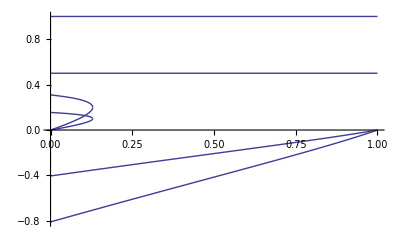

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->1/2/.R->1/2,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

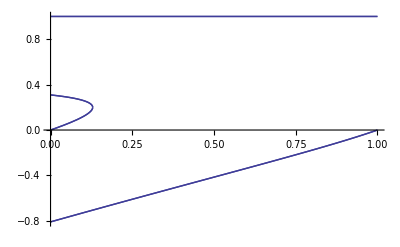

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->1/2/.R->0,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

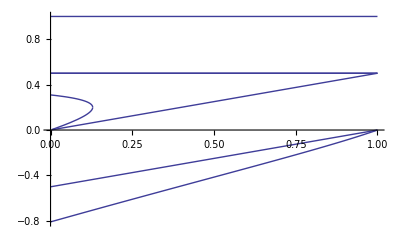

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->0/.R->1/2,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

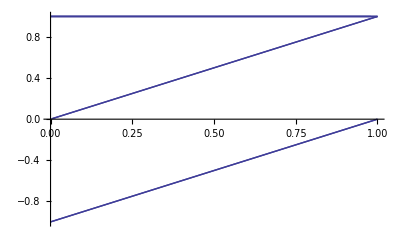

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->0/.R->0,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

And so it looks like on this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

And on the 2nd order (this takes a few minutes)

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{(dpAXmXf ((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) (1-pA+(-1+2 pA) h_female) sDip_female-(-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) (1-pA+(-1+2 pA) h_male) sDip_male+(-2 (1+k (-1+R))^2 R (1+(-1+k) R)+2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-k r^2 (-1+R) (-4+11 R-8 R^2+2 k^2 R (2-6 R+5 R^2)+k (4-21 R+30 R^2-10 R^3))+r (-2 (-1+R)^2+2 k^3 (1-2 R)^2 (-1+R) R+k (4-18 R+25 R^2-11 R^3)+k^2 (-2+16 R-39 R^2+35 R^3-8 R^4))) (sHap_female-sHap_male)))/(4 (-2+k) k^2 r^3 (2+k (-1+R)-R) (-1+R)^2 (-1+2 R)-2 R (5 (-2+R)+2 k^4 (-1+R)^3-k^3 (-1+R)^2 (-13+6 R)+k (29-35 R+9 R^2)+k^2 (-30+56 R-30 R^2+4 R^3))-2 k r^2 (-1+R) (20-41 R+17 R^2+k^2 (22-75 R+85 R^2-30 R^3)+2 k^3 (-2+8 R-11 R^2+5 R^3)+2 k (-19+53 R-45 R^2+10 R^3))+r (4 k^4 (1-3 R+2 R^2)^2+5 (5-8 R+3 R^2)+2 k (-35+96 R-89 R^2+24 R^3)-2 k^3 (14-69 R+124 R^2-93 R^3+24 R^4)+k^2 (69-266 R+371 R^2-202 R^3+32 R^4)))+(dpAYmXf ((2 k^2 r^3 (-1+R)^2 (-1+2 R) (1-2 k (-1+R)+k^2 (-1+2 R))+2 k R (-2+R-k^3 (-1+R)^2 (-1+2 R)+k (5-9 R+3 R^2)+2 k^2 (-2+6 R-5 R^2+R^3))+r (-2+2 k^4 (-1+R) (-1+2 R)^3-k (1-5 R+R^2)+k^2 (10-39 R+44 R^2-14 R^3)+k^3 (-9+48 R-91 R^2+70 R^3-16 R^4))+k r^2 (-4+9 R-4 R^2+k (-5+18 R-20 R^2+6 R^3)+k^3 (-4+24 R-54 R^2+54 R^3-20 R^4)+k^2 (13-63 R+110 R^2-80 R^3+20 R^4))) (1-pA+(-1+2 pA) h_female) sDip_female-(-1+k) (2 (-1+k) k^2 r^3 (-1+R)^2 (-1+2 R)-2 (-1+k) R (2+k^2 (-1+R)^2-R-k (3-4 R+R^2))+r (7+2 k^3 (1-2 R)^2 (-1+R)-8 R+3 R^2+k^2 (9-32 R+37 R^2-12 R^3)+k (-14+31 R-22 R^2+4 R^3))+k r^2 (8-19 R+12 R^2-2 R^3-2 k^2 (-2+8 R-11 R^2+5 R^3)+k (-11+35 R-36 R^2+12 R^3))) (1-pA+(-1+2 pA) h_male) sDip_male-2 r sHap_female+4 k r sHap_female-2 k^2 r sHap_female-4 k r^2 sHap_female+4 k^2 r^2 sHap_female-2 k^2 r^3 sHap_female+2 r R sHap_female-12 k r R sHap_female+12 k^2 r R sHap_female-2 k^3 r R sHap_female+13 k r^2 R sHap_female-23 k^2 r^2 R sHap_female+4 k^3 r^2 R sHap_female+10 k^2 r^3 R sHap_female-2 k^3 r^3 R sHap_female-4 k R^2 sHap_female+6 k^2 R^2 sHap_female-2 k^3 R^2 sHap_female+13 k r R^2 sHap_female-29 k^2 r R^2 sHap_female+10 k^3 r R^2 sHap_female-13 k r^2 R^2 sHap_female+45 k^2 r^2 R^2 sHap_female-16 k^3 r^2 R^2 sHap_female-18 k^2 r^3 R^2 sHap_female+8 k^3 r^3 R^2 sHap_female+2 k R^3 sHap_female-8 k^2 R^3 sHap_female+4 k^3 R^3 sHap_female-5 k r R^3 sHap_female+29 k^2 r R^3 sHap_female-16 k^3 r R^3 sHap_female+4 k r^2 R^3 sHap_female-36 k^2 r^2 R^3 sHap_female+22 k^3 r^2 R^3 sHap_female+14 k^2 r^3 R^3 sHap_female-10 k^3 r^3 R^3 sHap_female+2 k^2 R^4 sHap_female-2 k^3 R^4 sHap_female-8 k^2 r R^4 sHap_female+8 k^3 r R^4 sHap_female+10 k^2 r^2 R^4 sHap_female-10 k^3 r^2 R^4 sHap_female-4 k^2 r^3 R^4 sHap_female+4 k^3 r^3 R^4 sHap_female+7 r sHap_male-26 k r sHap_male+35 k^2 r sHap_male-20 k^3 r sHap_male+4 k^4 r sHap_male+8 k r^2 sHap_male-28 k^2 r^2 sHap_male+28 k^3 r^2 sHap_male-8 k^4 r^2 sHap_male+2 k^2 r^3 sHap_male-8 k^3 r^3 sHap_male+4 k^4 r^3 sHap_male+4 R sHap_male-18 k R sHap_male+28 k^2 R sHap_male-18 k^3 R sHap_male+4 k^4 R sHap_male-10 r R sHap_male+56 k r R sHap_male-114 k^2 r R sHap_male+92 k^3 r R sHap_male-24 k^4 r R sHap_male-23 k r^2 R sHap_male+95 k^2 r^2 R sHap_male-118 k^3 r^2 R sHap_male+40 k^4 r^2 R sHap_male-10 k^2 r^3 R sHap_male+38 k^3 r^3 R sHap_male-20 k^4 r^3 R sHap_male-2 R^2 sHap_male+18 k R^2 sHap_male-46 k^2 R^2 sHap_male+42 k^3 R^2 sHap_male-12 k^4 R^2 sHap_male+3 r R^2 sHap_male-39 k r R^2 sHap_male+132 k^2 r R^2 sHap_male-154 k^3 r R^2 sHap_male+52 k^4 r R^2 sHap_male+21 k r^2 R^2 sHap_male-113 k^2 r^2 R^2 sHap_male+184 k^3 r^2 R^2 sHap_male-76 k^4 r^2 R^2 sHap_male+18 k^2 r^3 R^2 sHap_male-64 k^3 r^3 R^2 sHap_male+36 k^4 r^3 R^2 sHap_male-4 k R^3 sHap_male+20 k^2 R^3 sHap_male-30 k^3 R^3 sHap_male+12 k^4 R^3 sHap_male+9 k r R^3 sHap_male-59 k^2 r R^3 sHap_male+106 k^3 r R^3 sHap_male-48 k^4 r R^3 sHap_male-6 k r^2 R^3 sHap_male+56 k^2 r^2 R^3 sHap_male-124 k^3 r^2 R^3 sHap_male+64 k^4 r^2 R^3 sHap_male-14 k^2 r^3 R^3 sHap_male+46 k^3 r^3 R^3 sHap_male-28 k^4 r^3 R^3 sHap_male-2 k^2 R^4 sHap_male+6 k^3 R^4 sHap_male-4 k^4 R^4 sHap_male+8 k^2 r R^4 sHap_male-24 k^3 r R^4 sHap_male+16 k^4 r R^4 sHap_male-10 k^2 r^2 R^4 sHap_male+30 k^3 r^2 R^4 sHap_male-20 k^4 r^2 R^4 sHap_male+4 k^2 r^3 R^4 sHap_male-12 k^3 r^3 R^4 sHap_male+8 k^4 r^3 R^4 sHap_male))/(4 (-2+k) k^2 r^3 (2+k (-1+R)-R) (-1+R)^2 (-1+2 R)-2 R (5 (-2+R)+2 k^4 (-1+R)^3-k^3 (-1+R)^2 (-13+6 R)+k (29-35 R+9 R^2)+k^2 (-30+56 R-30 R^2+4 R^3))-2 k r^2 (-1+R) (20-41 R+17 R^2+k^2 (22-75 R+85 R^2-30 R^3)+2 k^3 (-2+8 R-11 R^2+5 R^3)+2 k (-19+53 R-45 R^2+10 R^3))+r (4 k^4 (1-3 R+2 R^2)^2+5 (5-8 R+3 R^2)+2 k (-35+96 R-89 R^2+24 R^3)-2 k^3 (14-69 R+124 R^2-93 R^3+24 R^4)+k^2 (69-266 R+371 R^2-202 R^3+32 R^4)))+((-1+pA) pA (2 (2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-2 k r^2 (-1+R) (-2+5 R-3 R^2+k^2 R (2-6 R+5 R^2)+k (2-10 R+14 R^2-5 R^3))+R (2 (-1+R)-2 k^3 (-1+R)^2 R+k (4-9 R+3 R^2)+k^2 (-2+9 R-9 R^2+2 R^3))+r (-2+5 R+2 k^3 (1-2 R)^2 (-1+R) R-3 R^2+k (4-19 R+23 R^2-8 R^3)-2 k^2 (1-8 R+18 R^2-16 R^3+4 R^4))) (1-pA+(-1+2 pA) h_female)^2 sDip_female^2-(-1+k) (4 (-1+k) k^2 r^3 (-1+R)^3 (-1+2 R)-2 R (4+2 k^3 (-1+R)^3-3 R-k^2 (-1+R)^2 (-7+2 R)+k (-9+14 R-5 R^2))-2 (-1+k) k r^2 (-1+R)^2 (-6+9 R+2 k (2-6 R+5 R^2))+r (-1+R) (9+4 k^3 (1-2 R)^2 (-1+R)-9 R+k (-21+45 R-26 R^2)-2 k^2 (-8+27 R-29 R^2+8 R^3))) (-1+pA+(1-2 pA) h_male)^2 sDip_male^2-4 r sHap_female^2+8 k r sHap_female^2-4 k^2 r sHap_female^2-8 k r^2 sHap_female^2+8 k^2 r^2 sHap_female^2-4 k^2 r^3 sHap_female^2-4 R sHap_female^2+8 k R sHap_female^2-4 k^2 R sHap_female^2+8 r R sHap_female^2-30 k r R sHap_female^2+22 k^2 r R sHap_female^2+26 k r^2 R sHap_female^2-38 k^2 r^2 R sHap_female^2+20 k^2 r^3 R sHap_female^2+2 R^2 sHap_female^2-10 k R^2 sHap_female^2+8 k^2 R^2 sHap_female^2-6 r R^2 sHap_female^2+40 k r R^2 sHap_female^2-50 k^2 r R^2 sHap_female^2+4 k^3 r R^2 sHap_female^2-32 k r^2 R^2 sHap_female^2+84 k^2 r^2 R^2 sHap_female^2-8 k^3 r^2 R^2 sHap_female^2-40 k^2 r^3 R^2 sHap_female^2+4 k^3 r^3 R^2 sHap_female^2-2 R^3 sHap_female^2+10 k R^3 sHap_female^2-16 k^2 R^3 sHap_female^2+4 k^3 R^3 sHap_female^2+2 r R^3 sHap_female^2-24 k r R^3 sHap_female^2+70 k^2 r R^3 sHap_female^2-20 k^3 r R^3 sHap_female^2+22 k r^2 R^3 sHap_female^2-106 k^2 r^2 R^3 sHap_female^2+32 k^3 r^2 R^3 sHap_female^2+44 k^2 r^3 R^3 sHap_female^2-16 k^3 r^3 R^3 sHap_female^2-4 k R^4 sHap_female^2+16 k^2 R^4 sHap_female^2-8 k^3 R^4 sHap_female^2+10 k r R^4 sHap_female^2-58 k^2 r R^4 sHap_female^2+32 k^3 r R^4 sHap_female^2-8 k r^2 R^4 sHap_female^2+72 k^2 r^2 R^4 sHap_female^2-44 k^3 r^2 R^4 sHap_female^2-28 k^2 r^3 R^4 sHap_female^2+20 k^3 r^3 R^4 sHap_female^2-4 k^2 R^5 sHap_female^2+4 k^3 R^5 sHap_female^2+16 k^2 r R^5 sHap_female^2-16 k^3 r R^5 sHap_female^2-20 k^2 r^2 R^5 sHap_female^2+20 k^3 r^2 R^5 sHap_female^2+8 k^2 r^3 R^5 sHap_female^2-8 k^3 r^3 R^5 sHap_female^2-12 r sHap_female sHap_male+32 k r sHap_female sHap_male-28 k^2 r sHap_female sHap_male+8 k^3 r sHap_female sHap_male-20 k r^2 sHap_female sHap_male+36 k^2 r^2 sHap_female sHap_male-16 k^3 r^2 sHap_female sHap_male-8 k^2 r^3 sHap_female sHap_male+8 k^3 r^3 sHap_female sHap_male-8 R sHap_female sHap_male+24 k R sHap_female sHap_male-24 k^2 R sHap_female sHap_male+8 k^3 R sHap_female sHap_male+11 r R sHap_female sHap_male-64 k r R sHap_female sHap_male+85 k^2 r R sHap_female sHap_male-28 k^3 r R sHap_female sHap_male-4 k^4 r R sHap_female sHap_male+52 k r^2 R sHap_female sHap_male-112 k^2 r^2 R sHap_female sHap_male+52 k^3 r^2 R sHap_female sHap_male+8 k^4 r^2 R sHap_female sHap_male+32 k^2 r^3 R sHap_female sHap_male-32 k^3 r^3 R sHap_female sHap_male-4 k^4 r^3 R sHap_female sHap_male-16 k R^2 sHap_female sHap_male+26 k^2 R^2 sHap_female sHap_male-6 k^3 R^2 sHap_female sHap_male-4 k^4 R^2 sHap_female sHap_male+8 r R^2 sHap_female sHap_male+18 k r R^2 sHap_female sHap_male-56 k^2 r R^2 sHap_female sHap_male+6 k^3 r R^2 sHap_female sHap_male+24 k^4 r R^2 sHap_female sHap_male-22 k r^2 R^2 sHap_female sHap_male+72 k^2 r^2 R^2 sHap_female sHap_male-22 k^3 r^2 R^2 sHap_female sHap_male-40 k^4 r^2 R^2 sHap_female sHap_male-32 k^2 r^3 R^2 sHap_female sHap_male+28 k^3 r^3 R^2 sHap_female sHap_male+20 k^4 r^3 R^2 sHap_female sHap_male+6 R^3 sHap_female sHap_male-22 k R^3 sHap_female sHap_male+28 k^2 R^3 sHap_female sHap_male-24 k^3 R^3 sHap_female sHap_male+12 k^4 R^3 sHap_female sHap_male-7 r R^3 sHap_female sHap_male+44 k r R^3 sHap_female sHap_male-85 k^2 r R^3 sHap_female sHap_male+88 k^3 r R^3 sHap_female sHap_male-52 k^4 r R^3 sHap_female sHap_male-32 k r^2 R^3 sHap_female sHap_male+92 k^2 r^2 R^3 sHap_female sHap_male-104 k^3 r^2 R^3 sHap_female sHap_male+76 k^4 r^2 R^3 sHap_female sHap_male-16 k^2 r^3 R^3 sHap_female sHap_male+32 k^3 r^3 R^3 sHap_female sHap_male-36 k^4 r^3 R^3 sHap_female sHap_male+12 k R^4 sHap_female sHap_male-38 k^2 R^4 sHap_female sHap_male+34 k^3 R^4 sHap_female sHap_male-12 k^4 R^4 sHap_female sHap_male-30 k r R^4 sHap_female sHap_male+120 k^2 r R^4 sHap_female sHap_male-122 k^3 r R^4 sHap_female sHap_male+48 k^4 r R^4 sHap_female sHap_male+22 k r^2 R^4 sHap_female sHap_male-128 k^2 r^2 R^4 sHap_female sHap_male+150 k^3 r^2 R^4 sHap_female sHap_male-64 k^4 r^2 R^4 sHap_female sHap_male+40 k^2 r^3 R^4 sHap_female sHap_male-60 k^3 r^3 R^4 sHap_female sHap_male+28 k^4 r^3 R^4 sHap_female sHap_male+8 k^2 R^5 sHap_female sHap_male-12 k^3 R^5 sHap_female sHap_male+4 k^4 R^5 sHap_female sHap_male-32 k^2 r R^5 sHap_female sHap_male+48 k^3 r R^5 sHap_female sHap_male-16 k^4 r R^5 sHap_female sHap_male+40 k^2 r^2 R^5 sHap_female sHap_male-60 k^3 r^2 R^5 sHap_female sHap_male+20 k^4 r^2 R^5 sHap_female sHap_male-16 k^2 r^3 R^5 sHap_female sHap_male+24 k^3 r^3 R^5 sHap_female sHap_male-8 k^4 r^3 R^5 sHap_female sHap_male-9 r sHap_male^2+30 k r sHap_male^2-37 k^2 r sHap_male^2+20 k^3 r sHap_male^2-4 k^4 r sHap_male^2-12 k r^2 sHap_male^2+32 k^2 r^2 sHap_male^2-28 k^3 r^2 sHap_male^2+8 k^4 r^2 sHap_male^2-4 k^2 r^3 sHap_male^2+8 k^3 r^3 sHap_male^2-4 k^4 r^3 sHap_male^2-8 R sHap_male^2+26 k R sHap_male^2-32 k^2 R sHap_male^2+18 k^3 R sHap_male^2-4 k^4 R sHap_male^2+21 r R sHap_male^2-98 k r R sHap_male^2+159 k^2 r R sHap_male^2-110 k^3 r R sHap_male^2+28 k^4 r R sHap_male^2+44 k r^2 R sHap_male^2-138 k^2 r^2 R sHap_male^2+142 k^3 r^2 R sHap_male^2-48 k^4 r^2 R sHap_male^2+20 k^2 r^3 R sHap_male^2-44 k^3 r^3 R sHap_male^2+24 k^4 r^3 R sHap_male^2+8 R^2 sHap_male^2-44 k R^2 sHap_male^2+78 k^2 R^2 sHap_male^2-58 k^3 R^2 sHap_male^2+16 k^4 R^2 sHap_male^2-17 r R^2 sHap_male^2+120 k r R^2 sHap_male^2-265 k^2 r R^2 sHap_male^2+238 k^3 r R^2 sHap_male^2-76 k^4 r R^2 sHap_male^2-62 k r^2 R^2 sHap_male^2+236 k^2 r^2 R^2 sHap_male^2-290 k^3 r^2 R^2 sHap_male^2+116 k^4 r^2 R^2 sHap_male^2-40 k^2 r^3 R^2 sHap_male^2+96 k^3 r^3 R^2 sHap_male^2-56 k^4 r^3 R^2 sHap_male^2-4 R^3 sHap_male^2+30 k R^3 sHap_male^2-72 k^2 R^3 sHap_male^2+70 k^3 R^3 sHap_male^2-24 k^4 R^3 sHap_male^2+5 r R^3 sHap_male^2-68 k r R^3 sHap_male^2+217 k^2 r R^3 sHap_male^2-254 k^3 r R^3 sHap_male^2+100 k^4 r R^3 sHap_male^2+44 k r^2 R^3 sHap_male^2-206 k^2 r^2 R^3 sHap_male^2+302 k^3 r^2 R^3 sHap_male^2-140 k^4 r^2 R^3 sHap_male^2+44 k^2 r^3 R^3 sHap_male^2-108 k^3 r^3 R^3 sHap_male^2+64 k^4 r^3 R^3 sHap_male^2-8 k R^4 sHap_male^2+30 k^2 R^4 sHap_male^2-38 k^3 R^4 sHap_male^2+16 k^4 R^4 sHap_male^2+20 k r R^4 sHap_male^2-94 k^2 r R^4 sHap_male^2+138 k^3 r R^4 sHap_male^2-64 k^4 r R^4 sHap_male^2-14 k r^2 R^4 sHap_male^2+96 k^2 r^2 R^4 sHap_male^2-166 k^3 r^2 R^4 sHap_male^2+84 k^4 r^2 R^4 sHap_male^2-28 k^2 r^3 R^4 sHap_male^2+64 k^3 r^3 R^4 sHap_male^2-36 k^4 r^3 R^4 sHap_male^2-4 k^2 R^5 sHap_male^2+8 k^3 R^5 sHap_male^2-4 k^4 R^5 sHap_male^2+16 k^2 r R^5 sHap_male^2-32 k^3 r R^5 sHap_male^2+16 k^4 r R^5 sHap_male^2-20 k^2 r^2 R^5 sHap_male^2+40 k^3 r^2 R^5 sHap_male^2-20 k^4 r^2 R^5 sHap_male^2+8 k^2 r^3 R^5 sHap_male^2-16 k^3 r^3 R^5 sHap_male^2+8 k^4 r^3 R^5 sHap_male^2-2 (1-pA+(-1+2 pA) h_female) sDip_female ((-1+k) (4 k^2 r^3 (-1+R)^2 (-1+2 R)+R (-4-4 k^2 (-1+R)^2+k (8-9 R+R^2))-2 k r^2 (-1+R) (-5+8 R-R^2+2 k (2-6 R+5 R^2))+r (6 (-1+R)+4 k^2 (1-2 R)^2 (-1+R)+k (10-29 R+26 R^2-3 R^3))) (1-pA+(-1+2 pA) h_male) sDip_male+4 r sHap_female-8 k r sHap_female+4 k^2 r sHap_female+8 k r^2 sHap_female-8 k^2 r^2 sHap_female+4 k^2 r^3 sHap_female+4 R sHap_female-8 k R sHap_female+4 k^2 R sHap_female-4 r R sHap_female+17 k r R sHap_female-6 k^2 r R sHap_female-9 k^3 r R sHap_female+2 k^4 r R sHap_female-18 k r^2 R sHap_female+21 k^2 r^2 R sHap_female+13 k^3 r^2 R sHap_female-4 k^4 r^2 R sHap_female-16 k^2 r^3 R sHap_female-4 k^3 r^3 R sHap_female+2 k^4 r^3 R sHap_female+R^2 sHap_female+5 k^2 R^2 sHap_female-8 k^3 R^2 sHap_female+2 k^4 R^2 sHap_female-4 r R^2 sHap_female+11 k r R^2 sHap_female-31 k^2 r R^2 sHap_female+50 k^3 r R^2 sHap_female-14 k^4 r R^2 sHap_female+5 k^2 r^2 R^2 sHap_female-67 k^3 r^2 R^2 sHap_female+24 k^4 r^2 R^2 sHap_female+18 k^2 r^3 R^2 sHap_female+22 k^3 r^3 R^2 sHap_female-12 k^4 r^3 R^2 sHap_female-2 R^3 sHap_female+14 k R^3 sHap_female-26 k^2 R^3 sHap_female+26 k^3 R^3 sHap_female-8 k^4 R^3 sHap_female+3 r R^3 sHap_female-35 k r R^3 sHap_female+75 k^2 r R^3 sHap_female-101 k^3 r R^3 sHap_female+36 k^4 r R^3 sHap_female+20 k r^2 R^3 sHap_female-56 k^2 r^2 R^3 sHap_female+126 k^3 r^2 R^3 sHap_female-54 k^4 r^2 R^3 sHap_female-44 k^3 r^3 R^3 sHap_female+26 k^4 r^3 R^3 sHap_female-5 k R^4 sHap_female+17 k^2 R^4 sHap_female-24 k^3 R^4 sHap_female+10 k^4 R^4 sHap_female+14 k r R^4 sHap_female-52 k^2 r R^4 sHap_female+86 k^3 r R^4 sHap_female-40 k^4 r R^4 sHap_female-10 k r^2 R^4 sHap_female+48 k^2 r^2 R^4 sHap_female-102 k^3 r^2 R^4 sHap_female+54 k^4 r^2 R^4 sHap_female-10 k^2 r^3 R^4 sHap_female+38 k^3 r^3 R^4 sHap_female-24 k^4 r^3 R^4 sHap_female-2 k^2 R^5 sHap_female+6 k^3 R^5 sHap_female-4 k^4 R^5 sHap_female+8 k^2 r R^5 sHap_female-24 k^3 r R^5 sHap_female+16 k^4 r R^5 sHap_female-10 k^2 r^2 R^5 sHap_female+30 k^3 r^2 R^5 sHap_female-20 k^4 r^2 R^5 sHap_female+4 k^2 r^3 R^5 sHap_female-12 k^3 r^3 R^5 sHap_female+8 k^4 r^3 R^5 sHap_female+6 r sHap_male-16 k r sHap_male+14 k^2 r sHap_male-4 k^3 r sHap_male+10 k r^2 sHap_male-18 k^2 r^2 sHap_male+8 k^3 r^2 sHap_male+4 k^2 r^3 sHap_male-4 k^3 r^3 sHap_male+4 R sHap_male-12 k R sHap_male+12 k^2 R sHap_male-4 k^3 R sHap_male-12 r R sHap_male+56 k r R sHap_male-75 k^2 r R sHap_male+33 k^3 r R sHap_male-2 k^4 r R sHap_male-36 k r^2 R sHap_male+85 k^2 r^2 R sHap_male-53 k^3 r^2 R sHap_male+4 k^4 r^2 R sHap_male-20 k^2 r^3 R sHap_male+24 k^3 r^3 R sHap_male-2 k^4 r^3 R sHap_male-5 R^2 sHap_male+27 k R^2 sHap_male-40 k^2 R^2 sHap_male+20 k^3 R^2 sHap_male-2 k^4 R^2 sHap_male+10 r R^2 sHap_male-83 k r R^2 sHap_male+161 k^2 r R^2 sHap_male-102 k^3 r R^2 sHap_male+14 k^4 r R^2 sHap_male+50 k r^2 R^2 sHap_male-163 k^2 r^2 R^2 sHap_male+143 k^3 r^2 R^2 sHap_male-24 k^4 r^2 R^2 sHap_male+38 k^2 r^3 R^2 sHap_male-58 k^3 r^3 R^2 sHap_male+12 k^4 r^3 R^2 sHap_male+2 R^3 sHap_male-21 k R^3 sHap_male+49 k^2 R^3 sHap_male-38 k^3 R^3 sHap_male+8 k^4 R^3 sHap_male-3 r R^3 sHap_male+54 k r R^3 sHap_male-158 k^2 r R^3 sHap_male+149 k^3 r R^3 sHap_male-36 k^4 r R^3 sHap_male-34 k r^2 R^3 sHap_male+154 k^2 r^2 R^3 sHap_male-190 k^3 r^2 R^3 sHap_male+54 k^4 r^2 R^3 sHap_male-36 k^2 r^3 R^3 sHap_male+72 k^3 r^3 R^3 sHap_male-26 k^4 r^3 R^3 sHap_male+5 k R^4 sHap_male-21 k^2 R^4 sHap_male+28 k^3 R^4 sHap_male-10 k^4 R^4 sHap_male-14 k r R^4 sHap_male+68 k^2 r R^4 sHap_male-102 k^3 r R^4 sHap_male+40 k^4 r R^4 sHap_male+10 k r^2 R^4 sHap_male-68 k^2 r^2 R^4 sHap_male+122 k^3 r^2 R^4 sHap_male-54 k^4 r^2 R^4 sHap_male+18 k^2 r^3 R^4 sHap_male-46 k^3 r^3 R^4 sHap_male+24 k^4 r^3 R^4 sHap_male+2 k^2 R^5 sHap_male-6 k^3 R^5 sHap_male+4 k^4 R^5 sHap_male-8 k^2 r R^5 sHap_male+24 k^3 r R^5 sHap_male-16 k^4 r R^5 sHap_male+10 k^2 r^2 R^5 sHap_male-30 k^3 r^2 R^5 sHap_male+20 k^4 r^2 R^5 sHap_male-4 k^2 r^3 R^5 sHap_male+12 k^3 r^3 R^5 sHap_male-8 k^4 r^3 R^5 sHap_male)+(-1+k) (1-pA+(-1+2 pA) h_male) sDip_male ((4 k^2 r^3 (-1+R)^2 (-1+2 R) (-2+2 R+(-1+k) R^2)-2 k r^2 (-1+R) (10-24 R+19 R^2-7 R^3+2 k^2 R^2 (2-6 R+5 R^2)+k (-8+31 R-51 R^2+39 R^3-10 R^4))+2 R (4-3 R+R^2-2 k^3 (-1+R)^2 R^2+k (-8+15 R-12 R^2+3 R^3)+k^2 (4-11 R+16 R^2-11 R^3+2 R^4))+r (12-19 R+12 R^2+4 k^3 (1-2 R)^2 (-1+R) R^2-3 R^3+k (-20+71 R-108 R^2+71 R^3-18 R^4)-2 k^2 (-4+23 R-55 R^2+67 R^3-41 R^4+8 R^5))) sHap_female+(-4 k^2 r^3 (-1+R)^2 (-1+2 R) (2-R^2+k (-2+2 R+R^2))+2 R (8-3 R-R^2+k (-18+22 R+R^2-3 R^3)+k^2 (14-29 R+10 R^2+7 R^3-2 R^4)+2 k^3 (-2+6 R-5 R^2+R^4))+2 k r^2 (-1+R) (-12+22 R-R^2-7 R^3+k (20-55 R+31 R^2+19 R^3-10 R^4)+2 k^2 (-4+16 R-20 R^2+4 R^3+5 R^4))+r (18-29 R+6 R^2+3 R^3-4 k^3 (1-2 R)^2 (2-4 R+R^2+R^3)+k (-42+119 R-86 R^2-13 R^3+18 R^4)+2 k^2 (16-67 R+89 R^2-23 R^3-25 R^4+8 R^5))) sHap_male)))/(R (4 (-2+k) k^2 r^3 (2+k (-1+R)-R) (-1+R)^2 (-1+2 R)-2 R (5 (-2+R)+2 k^4 (-1+R)^3-k^3 (-1+R)^2 (-13+6 R)+k (29-35 R+9 R^2)+k^2 (-30+56 R-30 R^2+4 R^3))-2 k r^2 (-1+R) (20-41 R+17 R^2+k^2 (22-75 R+85 R^2-30 R^3)+2 k^3 (-2+8 R-11 R^2+5 R^3)+2 k (-19+53 R-45 R^2+10 R^3))+r (4 k^4 (1-3 R+2 R^2)^2+5 (5-8 R+3 R^2)+2 k (-35+96 R-89 R^2+24 R^3)-2 k^3 (14-69 R+124 R^2-93 R^3+24 R^4)+k^2 (69-266 R+371 R^2-202 R^3+32 R^4))))}

Then we can put in all the differences

```mathematica
tester=Collect[lambda2diffs/.realsol[[3]],{dpAXmXf,dpAYmXf},Simplify]
```

{(((-1+h_female) sDip_female+(-1+h_male) sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (-(-(sDip_female-sDip_male) (sHap_female+sHap_male)-2 h_male sDip_male (sDip_female+sHap_female+sHap_male)+2 h_female sDip_female (sDip_male+sHap_female+sHap_male)) ((-2 (1+k (-1+R))^2 R (1+(-1+k) R)+2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-k r^2 (-1+R) (-4+11 R-8 R^2+2 k^2 R (2-6 R+5 R^2)+k (4-21 R+30 R^2-10 R^3))+r (-2 (-1+R)^2+2 k^3 (1-2 R)^2 (-1+R) R+k (4-18 R+25 R^2-11 R^3)+k^2 (-2+16 R-39 R^2+35 R^3-8 R^4))) (sHap_female-sHap_male)-((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) sDip_male (h_female sDip_female+sHap_female+sHap_male-h_male (sDip_female+2 (sHap_female+sHap_male))))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)-((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) sDip_female (-h_male sDip_male-sHap_female-sHap_male+h_female (sDip_male+2 (sHap_female+sHap_male))))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male))-1/r(-r sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+r sDip_male sHap_male-h_male sDip_male (sDip_female+2 sHap_female-2 r sHap_female+2 r sHap_male)+h_female sDip_female (sDip_male+2 (r sHap_female+sHap_male-r sHap_male))) (-2 r sHap_female+4 k r sHap_female-2 k^2 r sHap_female-4 k r^2 sHap_female+4 k^2 r^2 sHap_female-2 k^2 r^3 sHap_female+2 r R sHap_female-12 k r R sHap_female+12 k^2 r R sHap_female-2 k^3 r R sHap_female+13 k r^2 R sHap_female-23 k^2 r^2 R sHap_female+4 k^3 r^2 R sHap_female+10 k^2 r^3 R sHap_female-2 k^3 r^3 R sHap_female-4 k R^2 sHap_female+6 k^2 R^2 sHap_female-2 k^3 R^2 sHap_female+13 k r R^2 sHap_female-29 k^2 r R^2 sHap_female+10 k^3 r R^2 sHap_female-13 k r^2 R^2 sHap_female+45 k^2 r^2 R^2 sHap_female-16 k^3 r^2 R^2 sHap_female-18 k^2 r^3 R^2 sHap_female+8 k^3 r^3 R^2 sHap_female+2 k R^3 sHap_female-8 k^2 R^3 sHap_female+4 k^3 R^3 sHap_female-5 k r R^3 sHap_female+29 k^2 r R^3 sHap_female-16 k^3 r R^3 sHap_female+4 k r^2 R^3 sHap_female-36 k^2 r^2 R^3 sHap_female+22 k^3 r^2 R^3 sHap_female+14 k^2 r^3 R^3 sHap_female-10 k^3 r^3 R^3 sHap_female+2 k^2 R^4 sHap_female-2 k^3 R^4 sHap_female-8 k^2 r R^4 sHap_female+8 k^3 r R^4 sHap_female+10 k^2 r^2 R^4 sHap_female-10 k^3 r^2 R^4 sHap_female-4 k^2 r^3 R^4 sHap_female+4 k^3 r^3 R^4 sHap_female+7 r sHap_male-26 k r sHap_male+35 k^2 r sHap_male-20 k^3 r sHap_male+4 k^4 r sHap_male+8 k r^2 sHap_male-28 k^2 r^2 sHap_male+28 k^3 r^2 sHap_male-8 k^4 r^2 sHap_male+2 k^2 r^3 sHap_male-8 k^3 r^3 sHap_male+4 k^4 r^3 sHap_male+4 R sHap_male-18 k R sHap_male+28 k^2 R sHap_male-18 k^3 R sHap_male+4 k^4 R sHap_male-10 r R sHap_male+56 k r R sHap_male-114 k^2 r R sHap_male+92 k^3 r R sHap_male-24 k^4 r R sHap_male-23 k r^2 R sHap_male+95 k^2 r^2 R sHap_male-118 k^3 r^2 R sHap_male+40 k^4 r^2 R sHap_male-10 k^2 r^3 R sHap_male+38 k^3 r^3 R sHap_male-20 k^4 r^3 R sHap_male-2 R^2 sHap_male+18 k R^2 sHap_male-46 k^2 R^2 sHap_male+42 k^3 R^2 sHap_male-12 k^4 R^2 sHap_male+3 r R^2 sHap_male-39 k r R^2 sHap_male+132 k^2 r R^2 sHap_male-154 k^3 r R^2 sHap_male+52 k^4 r R^2 sHap_male+21 k r^2 R^2 sHap_male-113 k^2 r^2 R^2 sHap_male+184 k^3 r^2 R^2 sHap_male-76 k^4 r^2 R^2 sHap_male+18 k^2 r^3 R^2 sHap_male-64 k^3 r^3 R^2 sHap_male+36 k^4 r^3 R^2 sHap_male-4 k R^3 sHap_male+20 k^2 R^3 sHap_male-30 k^3 R^3 sHap_male+12 k^4 R^3 sHap_male+9 k r R^3 sHap_male-59 k^2 r R^3 sHap_male+106 k^3 r R^3 sHap_male-48 k^4 r R^3 sHap_male-6 k r^2 R^3 sHap_male+56 k^2 r^2 R^3 sHap_male-124 k^3 r^2 R^3 sHap_male+64 k^4 r^2 R^3 sHap_male-14 k^2 r^3 R^3 sHap_male+46 k^3 r^3 R^3 sHap_male-28 k^4 r^3 R^3 sHap_male-2 k^2 R^4 sHap_male+6 k^3 R^4 sHap_male-4 k^4 R^4 sHap_male+8 k^2 r R^4 sHap_male-24 k^3 r R^4 sHap_male+16 k^4 r R^4 sHap_male-10 k^2 r^2 R^4 sHap_male+30 k^3 r^2 R^4 sHap_male-20 k^4 r^2 R^4 sHap_male+4 k^2 r^3 R^4 sHap_male-12 k^3 r^3 R^4 sHap_male+8 k^4 r^3 R^4 sHap_male-((-1+k) (2 (-1+k) k^2 r^3 (-1+R)^2 (-1+2 R)-2 (-1+k) R (2+k^2 (-1+R)^2-R-k (3-4 R+R^2))+r (7+2 k^3 (1-2 R)^2 (-1+R)-8 R+3 R^2+k^2 (9-32 R+37 R^2-12 R^3)+k (-14+31 R-22 R^2+4 R^3))+k r^2 (8-19 R+12 R^2-2 R^3-2 k^2 (-2+8 R-11 R^2+5 R^3)+k (-11+35 R-36 R^2+12 R^3))) sDip_male (h_female sDip_female+sHap_female+sHap_male-h_male (sDip_female+2 (sHap_female+sHap_male))))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)-((2 k^2 r^3 (-1+R)^2 (-1+2 R) (1-2 k (-1+R)+k^2 (-1+2 R))+2 k R (-2+R-k^3 (-1+R)^2 (-1+2 R)+k (5-9 R+3 R^2)+2 k^2 (-2+6 R-5 R^2+R^3))+r (-2+2 k^4 (-1+R) (-1+2 R)^3-k (1-5 R+R^2)+k^2 (10-39 R+44 R^2-14 R^3)+k^3 (-9+48 R-91 R^2+70 R^3-16 R^4))+k r^2 (-4+9 R-4 R^2+k (-5+18 R-20 R^2+6 R^3)+k^3 (-4+24 R-54 R^2+54 R^3-20 R^4)+k^2 (13-63 R+110 R^2-80 R^3+20 R^4))) sDip_female (-h_male sDip_male-sHap_female-sHap_male+h_female (sDip_male+2 (sHap_female+sHap_male))))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male))+(((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^2 (-4 r sHap_female^2+8 k r sHap_female^2-4 k^2 r sHap_female^2-8 k r^2 sHap_female^2+8 k^2 r^2 sHap_female^2-4 k^2 r^3 sHap_female^2-4 R sHap_female^2+8 k R sHap_female^2-4 k^2 R sHap_female^2+8 r R sHap_female^2-30 k r R sHap_female^2+22 k^2 r R sHap_female^2+26 k r^2 R sHap_female^2-38 k^2 r^2 R sHap_female^2+20 k^2 r^3 R sHap_female^2+2 R^2 sHap_female^2-10 k R^2 sHap_female^2+8 k^2 R^2 sHap_female^2-6 r R^2 sHap_female^2+40 k r R^2 sHap_female^2-50 k^2 r R^2 sHap_female^2+4 k^3 r R^2 sHap_female^2-32 k r^2 R^2 sHap_female^2+84 k^2 r^2 R^2 sHap_female^2-8 k^3 r^2 R^2 sHap_female^2-40 k^2 r^3 R^2 sHap_female^2+4 k^3 r^3 R^2 sHap_female^2-2 R^3 sHap_female^2+10 k R^3 sHap_female^2-16 k^2 R^3 sHap_female^2+4 k^3 R^3 sHap_female^2+2 r R^3 sHap_female^2-24 k r R^3 sHap_female^2+70 k^2 r R^3 sHap_female^2-20 k^3 r R^3 sHap_female^2+22 k r^2 R^3 sHap_female^2-106 k^2 r^2 R^3 sHap_female^2+32 k^3 r^2 R^3 sHap_female^2+44 k^2 r^3 R^3 sHap_female^2-16 k^3 r^3 R^3 sHap_female^2-4 k R^4 sHap_female^2+16 k^2 R^4 sHap_female^2-8 k^3 R^4 sHap_female^2+10 k r R^4 sHap_female^2-58 k^2 r R^4 sHap_female^2+32 k^3 r R^4 sHap_female^2-8 k r^2 R^4 sHap_female^2+72 k^2 r^2 R^4 sHap_female^2-44 k^3 r^2 R^4 sHap_female^2-28 k^2 r^3 R^4 sHap_female^2+20 k^3 r^3 R^4 sHap_female^2-4 k^2 R^5 sHap_female^2+4 k^3 R^5 sHap_female^2+16 k^2 r R^5 sHap_female^2-16 k^3 r R^5 sHap_female^2-20 k^2 r^2 R^5 sHap_female^2+20 k^3 r^2 R^5 sHap_female^2+8 k^2 r^3 R^5 sHap_female^2-8 k^3 r^3 R^5 sHap_female^2-12 r sHap_female sHap_male+32 k r sHap_female sHap_male-28 k^2 r sHap_female sHap_male+8 k^3 r sHap_female sHap_male-20 k r^2 sHap_female sHap_male+36 k^2 r^2 sHap_female sHap_male-16 k^3 r^2 sHap_female sHap_male-8 k^2 r^3 sHap_female sHap_male+8 k^3 r^3 sHap_female sHap_male-8 R sHap_female sHap_male+24 k R sHap_female sHap_male-24 k^2 R sHap_female sHap_male+8 k^3 R sHap_female sHap_male+11 r R sHap_female sHap_male-64 k r R sHap_female sHap_male+85 k^2 r R sHap_female sHap_male-28 k^3 r R sHap_female sHap_male-4 k^4 r R sHap_female sHap_male+52 k r^2 R sHap_female sHap_male-112 k^2 r^2 R sHap_female sHap_male+52 k^3 r^2 R sHap_female sHap_male+8 k^4 r^2 R sHap_female sHap_male+32 k^2 r^3 R sHap_female sHap_male-32 k^3 r^3 R sHap_female sHap_male-4 k^4 r^3 R sHap_female sHap_male-16 k R^2 sHap_female sHap_male+26 k^2 R^2 sHap_female sHap_male-6 k^3 R^2 sHap_female sHap_male-4 k^4 R^2 sHap_female sHap_male+8 r R^2 sHap_female sHap_male+18 k r R^2 sHap_female sHap_male-56 k^2 r R^2 sHap_female sHap_male+6 k^3 r R^2 sHap_female sHap_male+24 k^4 r R^2 sHap_female sHap_male-22 k r^2 R^2 sHap_female sHap_male+72 k^2 r^2 R^2 sHap_female sHap_male-22 k^3 r^2 R^2 sHap_female sHap_male-40 k^4 r^2 R^2 sHap_female sHap_male-32 k^2 r^3 R^2 sHap_female sHap_male+28 k^3 r^3 R^2 sHap_female sHap_male+20 k^4 r^3 R^2 sHap_female sHap_male+6 R^3 sHap_female sHap_male-22 k R^3 sHap_female sHap_male+28 k^2 R^3 sHap_female sHap_male-24 k^3 R^3 sHap_female sHap_male+12 k^4 R^3 sHap_female sHap_male-7 r R^3 sHap_female sHap_male+44 k r R^3 sHap_female sHap_male-85 k^2 r R^3 sHap_female sHap_male+88 k^3 r R^3 sHap_female sHap_male-52 k^4 r R^3 sHap_female sHap_male-32 k r^2 R^3 sHap_female sHap_male+92 k^2 r^2 R^3 sHap_female sHap_male-104 k^3 r^2 R^3 sHap_female sHap_male+76 k^4 r^2 R^3 sHap_female sHap_male-16 k^2 r^3 R^3 sHap_female sHap_male+32 k^3 r^3 R^3 sHap_female sHap_male-36 k^4 r^3 R^3 sHap_female sHap_male+12 k R^4 sHap_female sHap_male-38 k^2 R^4 sHap_female sHap_male+34 k^3 R^4 sHap_female sHap_male-12 k^4 R^4 sHap_female sHap_male-30 k r R^4 sHap_female sHap_male+120 k^2 r R^4 sHap_female sHap_male-122 k^3 r R^4 sHap_female sHap_male+48 k^4 r R^4 sHap_female sHap_male+22 k r^2 R^4 sHap_female sHap_male-128 k^2 r^2 R^4 sHap_female sHap_male+150 k^3 r^2 R^4 sHap_female sHap_male-64 k^4 r^2 R^4 sHap_female sHap_male+40 k^2 r^3 R^4 sHap_female sHap_male-60 k^3 r^3 R^4 sHap_female sHap_male+28 k^4 r^3 R^4 sHap_female sHap_male+8 k^2 R^5 sHap_female sHap_male-12 k^3 R^5 sHap_female sHap_male+4 k^4 R^5 sHap_female sHap_male-32 k^2 r R^5 sHap_female sHap_male+48 k^3 r R^5 sHap_female sHap_male-16 k^4 r R^5 sHap_female sHap_male+40 k^2 r^2 R^5 sHap_female sHap_male-60 k^3 r^2 R^5 sHap_female sHap_male+20 k^4 r^2 R^5 sHap_female sHap_male-16 k^2 r^3 R^5 sHap_female sHap_male+24 k^3 r^3 R^5 sHap_female sHap_male-8 k^4 r^3 R^5 sHap_female sHap_male-9 r sHap_male^2+30 k r sHap_male^2-37 k^2 r sHap_male^2+20 k^3 r sHap_male^2-4 k^4 r sHap_male^2-12 k r^2 sHap_male^2+32 k^2 r^2 sHap_male^2-28 k^3 r^2 sHap_male^2+8 k^4 r^2 sHap_male^2-4 k^2 r^3 sHap_male^2+8 k^3 r^3 sHap_male^2-4 k^4 r^3 sHap_male^2-8 R sHap_male^2+26 k R sHap_male^2-32 k^2 R sHap_male^2+18 k^3 R sHap_male^2-4 k^4 R sHap_male^2+21 r R sHap_male^2-98 k r R sHap_male^2+159 k^2 r R sHap_male^2-110 k^3 r R sHap_male^2+28 k^4 r R sHap_male^2+44 k r^2 R sHap_male^2-138 k^2 r^2 R sHap_male^2+142 k^3 r^2 R sHap_male^2-48 k^4 r^2 R sHap_male^2+20 k^2 r^3 R sHap_male^2-44 k^3 r^3 R sHap_male^2+24 k^4 r^3 R sHap_male^2+8 R^2 sHap_male^2-44 k R^2 sHap_male^2+78 k^2 R^2 sHap_male^2-58 k^3 R^2 sHap_male^2+16 k^4 R^2 sHap_male^2-17 r R^2 sHap_male^2+120 k r R^2 sHap_male^2-265 k^2 r R^2 sHap_male^2+238 k^3 r R^2 sHap_male^2-76 k^4 r R^2 sHap_male^2-62 k r^2 R^2 sHap_male^2+236 k^2 r^2 R^2 sHap_male^2-290 k^3 r^2 R^2 sHap_male^2+116 k^4 r^2 R^2 sHap_male^2-40 k^2 r^3 R^2 sHap_male^2+96 k^3 r^3 R^2 sHap_male^2-56 k^4 r^3 R^2 sHap_male^2-4 R^3 sHap_male^2+30 k R^3 sHap_male^2-72 k^2 R^3 sHap_male^2+70 k^3 R^3 sHap_male^2-24 k^4 R^3 sHap_male^2+5 r R^3 sHap_male^2-68 k r R^3 sHap_male^2+217 k^2 r R^3 sHap_male^2-254 k^3 r R^3 sHap_male^2+100 k^4 r R^3 sHap_male^2+44 k r^2 R^3 sHap_male^2-206 k^2 r^2 R^3 sHap_male^2+302 k^3 r^2 R^3 sHap_male^2-140 k^4 r^2 R^3 sHap_male^2+44 k^2 r^3 R^3 sHap_male^2-108 k^3 r^3 R^3 sHap_male^2+64 k^4 r^3 R^3 sHap_male^2-8 k R^4 sHap_male^2+30 k^2 R^4 sHap_male^2-38 k^3 R^4 sHap_male^2+16 k^4 R^4 sHap_male^2+20 k r R^4 sHap_male^2-94 k^2 r R^4 sHap_male^2+138 k^3 r R^4 sHap_male^2-64 k^4 r R^4 sHap_male^2-14 k r^2 R^4 sHap_male^2+96 k^2 r^2 R^4 sHap_male^2-166 k^3 r^2 R^4 sHap_male^2+84 k^4 r^2 R^4 sHap_male^2-28 k^2 r^3 R^4 sHap_male^2+64 k^3 r^3 R^4 sHap_male^2-36 k^4 r^3 R^4 sHap_male^2-4 k^2 R^5 sHap_male^2+8 k^3 R^5 sHap_male^2-4 k^4 R^5 sHap_male^2+16 k^2 r R^5 sHap_male^2-32 k^3 r R^5 sHap_male^2+16 k^4 r R^5 sHap_male^2-20 k^2 r^2 R^5 sHap_male^2+40 k^3 r^2 R^5 sHap_male^2-20 k^4 r^2 R^5 sHap_male^2+8 k^2 r^3 R^5 sHap_male^2-16 k^3 r^3 R^5 sHap_male^2+8 k^4 r^3 R^5 sHap_male^2+((-1+k) sDip_male ((4 k^2 r^3 (-1+R)^2 (-1+2 R) (-2+2 R+(-1+k) R^2)-2 k r^2 (-1+R) (10-24 R+19 R^2-7 R^3+2 k^2 R^2 (2-6 R+5 R^2)+k (-8+31 R-51 R^2+39 R^3-10 R^4))+2 R (4-3 R+R^2-2 k^3 (-1+R)^2 R^2+k (-8+15 R-12 R^2+3 R^3)+k^2 (4-11 R+16 R^2-11 R^3+2 R^4))+r (12-19 R+12 R^2+4 k^3 (1-2 R)^2 (-1+R) R^2-3 R^3+k (-20+71 R-108 R^2+71 R^3-18 R^4)-2 k^2 (-4+23 R-55 R^2+67 R^3-41 R^4+8 R^5))) sHap_female+(-4 k^2 r^3 (-1+R)^2 (-1+2 R) (2-R^2+k (-2+2 R+R^2))+2 R (8-3 R-R^2+k (-18+22 R+R^2-3 R^3)+k^2 (14-29 R+10 R^2+7 R^3-2 R^4)+2 k^3 (-2+6 R-5 R^2+R^4))+2 k r^2 (-1+R) (-12+22 R-R^2-7 R^3+k (20-55 R+31 R^2+19 R^3-10 R^4)+2 k^2 (-4+16 R-20 R^2+4 R^3+5 R^4))+r (18-29 R+6 R^2+3 R^3-4 k^3 (1-2 R)^2 (2-4 R+R^2+R^3)+k (-42+119 R-86 R^2-13 R^3+18 R^4)+2 k^2 (16-67 R+89 R^2-23 R^3-25 R^4+8 R^5))) sHap_male) (h_female sDip_female+sHap_female+sHap_male-h_male (sDip_female+2 (sHap_female+sHap_male))))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)-((-1+k) (4 (-1+k) k^2 r^3 (-1+R)^3 (-1+2 R)-2 R (4+2 k^3 (-1+R)^3-3 R-k^2 (-1+R)^2 (-7+2 R)+k (-9+14 R-5 R^2))-2 (-1+k) k r^2 (-1+R)^2 (-6+9 R+2 k (2-6 R+5 R^2))+r (-1+R) (9+4 k^3 (1-2 R)^2 (-1+R)-9 R+k (-21+45 R-26 R^2)-2 k^2 (-8+27 R-29 R^2+8 R^3))) sDip_male^2 (h_female sDip_female+sHap_female+sHap_male-h_male (sDip_female+2 (sHap_female+sHap_male)))^2)/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^2+(2 (2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-2 k r^2 (-1+R) (-2+5 R-3 R^2+k^2 R (2-6 R+5 R^2)+k (2-10 R+14 R^2-5 R^3))+R (2 (-1+R)-2 k^3 (-1+R)^2 R+k (4-9 R+3 R^2)+k^2 (-2+9 R-9 R^2+2 R^3))+r (-2+5 R+2 k^3 (1-2 R)^2 (-1+R) R-3 R^2+k (4-19 R+23 R^2-8 R^3)-2 k^2 (1-8 R+18 R^2-16 R^3+4 R^4))) sDip_female^2 (h_male sDip_male+sHap_female+sHap_male-h_female (sDip_male+2 (sHap_female+sHap_male)))^2)/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^2-(2 sDip_female (h_male sDip_male+sHap_female+sHap_male-h_female (sDip_male+2 (sHap_female+sHap_male))) (4 r sHap_female-8 k r sHap_female+4 k^2 r sHap_female+8 k r^2 sHap_female-8 k^2 r^2 sHap_female+4 k^2 r^3 sHap_female+4 R sHap_female-8 k R sHap_female+4 k^2 R sHap_female-4 r R sHap_female+17 k r R sHap_female-6 k^2 r R sHap_female-9 k^3 r R sHap_female+2 k^4 r R sHap_female-18 k r^2 R sHap_female+21 k^2 r^2 R sHap_female+13 k^3 r^2 R sHap_female-4 k^4 r^2 R sHap_female-16 k^2 r^3 R sHap_female-4 k^3 r^3 R sHap_female+2 k^4 r^3 R sHap_female+R^2 sHap_female+5 k^2 R^2 sHap_female-8 k^3 R^2 sHap_female+2 k^4 R^2 sHap_female-4 r R^2 sHap_female+11 k r R^2 sHap_female-31 k^2 r R^2 sHap_female+50 k^3 r R^2 sHap_female-14 k^4 r R^2 sHap_female+5 k^2 r^2 R^2 sHap_female-67 k^3 r^2 R^2 sHap_female+24 k^4 r^2 R^2 sHap_female+18 k^2 r^3 R^2 sHap_female+22 k^3 r^3 R^2 sHap_female-12 k^4 r^3 R^2 sHap_female-2 R^3 sHap_female+14 k R^3 sHap_female-26 k^2 R^3 sHap_female+26 k^3 R^3 sHap_female-8 k^4 R^3 sHap_female+3 r R^3 sHap_female-35 k r R^3 sHap_female+75 k^2 r R^3 sHap_female-101 k^3 r R^3 sHap_female+36 k^4 r R^3 sHap_female+20 k r^2 R^3 sHap_female-56 k^2 r^2 R^3 sHap_female+126 k^3 r^2 R^3 sHap_female-54 k^4 r^2 R^3 sHap_female-44 k^3 r^3 R^3 sHap_female+26 k^4 r^3 R^3 sHap_female-5 k R^4 sHap_female+17 k^2 R^4 sHap_female-24 k^3 R^4 sHap_female+10 k^4 R^4 sHap_female+14 k r R^4 sHap_female-52 k^2 r R^4 sHap_female+86 k^3 r R^4 sHap_female-40 k^4 r R^4 sHap_female-10 k r^2 R^4 sHap_female+48 k^2 r^2 R^4 sHap_female-102 k^3 r^2 R^4 sHap_female+54 k^4 r^2 R^4 sHap_female-10 k^2 r^3 R^4 sHap_female+38 k^3 r^3 R^4 sHap_female-24 k^4 r^3 R^4 sHap_female-2 k^2 R^5 sHap_female+6 k^3 R^5 sHap_female-4 k^4 R^5 sHap_female+8 k^2 r R^5 sHap_female-24 k^3 r R^5 sHap_female+16 k^4 r R^5 sHap_female-10 k^2 r^2 R^5 sHap_female+30 k^3 r^2 R^5 sHap_female-20 k^4 r^2 R^5 sHap_female+4 k^2 r^3 R^5 sHap_female-12 k^3 r^3 R^5 sHap_female+8 k^4 r^3 R^5 sHap_female+6 r sHap_male-16 k r sHap_male+14 k^2 r sHap_male-4 k^3 r sHap_male+10 k r^2 sHap_male-18 k^2 r^2 sHap_male+8 k^3 r^2 sHap_male+4 k^2 r^3 sHap_male-4 k^3 r^3 sHap_male+4 R sHap_male-12 k R sHap_male+12 k^2 R sHap_male-4 k^3 R sHap_male-12 r R sHap_male+56 k r R sHap_male-75 k^2 r R sHap_male+33 k^3 r R sHap_male-2 k^4 r R sHap_male-36 k r^2 R sHap_male+85 k^2 r^2 R sHap_male-53 k^3 r^2 R sHap_male+4 k^4 r^2 R sHap_male-20 k^2 r^3 R sHap_male+24 k^3 r^3 R sHap_male-2 k^4 r^3 R sHap_male-5 R^2 sHap_male+27 k R^2 sHap_male-40 k^2 R^2 sHap_male+20 k^3 R^2 sHap_male-2 k^4 R^2 sHap_male+10 r R^2 sHap_male-83 k r R^2 sHap_male+161 k^2 r R^2 sHap_male-102 k^3 r R^2 sHap_male+14 k^4 r R^2 sHap_male+50 k r^2 R^2 sHap_male-163 k^2 r^2 R^2 sHap_male+143 k^3 r^2 R^2 sHap_male-24 k^4 r^2 R^2 sHap_male+38 k^2 r^3 R^2 sHap_male-58 k^3 r^3 R^2 sHap_male+12 k^4 r^3 R^2 sHap_male+2 R^3 sHap_male-21 k R^3 sHap_male+49 k^2 R^3 sHap_male-38 k^3 R^3 sHap_male+8 k^4 R^3 sHap_male-3 r R^3 sHap_male+54 k r R^3 sHap_male-158 k^2 r R^3 sHap_male+149 k^3 r R^3 sHap_male-36 k^4 r R^3 sHap_male-34 k r^2 R^3 sHap_male+154 k^2 r^2 R^3 sHap_male-190 k^3 r^2 R^3 sHap_male+54 k^4 r^2 R^3 sHap_male-36 k^2 r^3 R^3 sHap_male+72 k^3 r^3 R^3 sHap_male-26 k^4 r^3 R^3 sHap_male+5 k R^4 sHap_male-21 k^2 R^4 sHap_male+28 k^3 R^4 sHap_male-10 k^4 R^4 sHap_male-14 k r R^4 sHap_male+68 k^2 r R^4 sHap_male-102 k^3 r R^4 sHap_male+40 k^4 r R^4 sHap_male+10 k r^2 R^4 sHap_male-68 k^2 r^2 R^4 sHap_male+122 k^3 r^2 R^4 sHap_male-54 k^4 r^2 R^4 sHap_male+18 k^2 r^3 R^4 sHap_male-46 k^3 r^3 R^4 sHap_male+24 k^4 r^3 R^4 sHap_male+2 k^2 R^5 sHap_male-6 k^3 R^5 sHap_male+4 k^4 R^5 sHap_male-8 k^2 r R^5 sHap_male+24 k^3 r R^5 sHap_male-16 k^4 r R^5 sHap_male+10 k^2 r^2 R^5 sHap_male-30 k^3 r^2 R^5 sHap_male+20 k^4 r^2 R^5 sHap_male-4 k^2 r^3 R^5 sHap_male+12 k^3 r^3 R^5 sHap_male-8 k^4 r^3 R^5 sHap_male+((-1+k) (4 k^2 r^3 (-1+R)^2 (-1+2 R)+R (-4-4 k^2 (-1+R)^2+k (8-9 R+R^2))-2 k r^2 (-1+R) (-5+8 R-R^2+2 k (2-6 R+5 R^2))+r (6 (-1+R)+4 k^2 (1-2 R)^2 (-1+R)+k (10-29 R+26 R^2-3 R^3))) sDip_male (h_female sDip_female+sHap_female+sHap_male-h_male (sDip_female+2 (sHap_female+sHap_male))))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)))/((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)))/(R ((1-2 h_female) sDip_female+(1-2 h_male) sDip_male))))/((4 (-2+k) k^2 r^3 (2+k (-1+R)-R) (-1+R)^2 (-1+2 R)-2 R (5 (-2+R)+2 k^4 (-1+R)^3-k^3 (-1+R)^2 (-13+6 R)+k (29-35 R+9 R^2)+k^2 (-30+56 R-30 R^2+4 R^3))-2 k r^2 (-1+R) (20-41 R+17 R^2+k^2 (22-75 R+85 R^2-30 R^3)+2 k^3 (-2+8 R-11 R^2+5 R^3)+2 k (-19+53 R-45 R^2+10 R^3))+r (4 k^4 (1-3 R+2 R^2)^2+5 (5-8 R+3 R^2)+2 k (-35+96 R-89 R^2+24 R^3)-2 k^3 (14-69 R+124 R^2-93 R^3+24 R^4)+k^2 (69-266 R+371 R^2-202 R^3+32 R^4))) ((-1+2 h_female) sDip_female+(-1+2 h_male) sDip_male)^3)}

This reduces in some special cases

```mathematica
Collect[tester/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->0,Subscript[sHap, male],FullSimplify]
```

{((-1+h) h sDip_female ((2 (-2+R) R^2+r R (-5+(16-7 R) R)+r^2 (-1+R) (-1+R (-9+8 R))) sDip_female-2 r (4 r (-1+R)-3 R) R (-1+2 R) sDip_male) sHap_male^2)/(5 (1-2 h)^2 r R (-2 (-2+R) R+r (-1+R) (-5+3 R)) (sDip_female+sDip_male)^2)+(sDip_female (-(2 (-2+R) R^2+r R (-5+(16-7 R) R)+r^2 (-1+R) (-1+R (-9+8 R))) sDip_female+2 r (4 r (-1+R)-3 R) R (-1+2 R) sDip_male) sHap_male^3)/(5 (1-2 h)^2 r R (-2 (-2+R) R+r (-1+R) (-5+3 R)) (sDip_female+sDip_male)^3)+(sDip_female (-(2 (-2+R) R^2+r R (-5+(16-7 R) R)+r^2 (-1+R) (-1+R (-9+8 R))) sDip_female+2 r (4 r (-1+R)-3 R) R (-1+2 R) sDip_male) sHap_male^4)/(5 (1-2 h)^2 r R (-2 (-2+R) R+r (-1+R) (-5+3 R)) (sDip_female+sDip_male)^4)}

```mathematica
Collect[tester/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->1,{Subscript[sHap, male]},FullSimplify]
```

{-((-1+h) h sDip_female ((2 r (-1+R)+R) sDip_female+(-1+2 r) R sDip_male) sHap_male^2)/(2 (1-2 h)^2 r R (sDip_female+sDip_male)^2)+(sDip_female ((2 r (-1+R)+R) sDip_female+(-1+2 r) R sDip_male) sHap_male^3)/(2 (1-2 h)^2 r R (sDip_female+sDip_male)^3)+(sDip_female ((2 r (-1+R)+R) sDip_female+(-1+2 r) R sDip_male) sHap_male^4)/(2 (1-2 h)^2 r R (sDip_female+sDip_male)^4)}

```mathematica
Collect[tester/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.k->1/2,Subscript[sHap, male],FullSimplify]
```

{-((-1+h) h sDip_female ((-2 r^4+r (4+r (5+r (-23+4 r))) R+(3+r (9+r (-59+6 r (7+r)))) R^2+(8+r (-27-r (1+r) (-29+16 r))) R^3+(3+r (-22+r (41+8 (-4+r) r))) R^4+2 (-1+r)^2 (-1+2 r) R^5) sDip_female+R ((-3+R) R (1+R)+2 r^4 (-1+R)^2 (5+2 R (-7+4 R))+r (-4+R (3+R (15-2 R (1+4 R))))+r^3 (15-R (22+R (45+8 R (-11+5 R))))+r^2 (1+R (25+R (-21+R (-35+32 R))))) sDip_male) sHap_male^2)/(2 (1-2 h)^2 r R (-4-3 R+r (-3+6 R)) (r^2 (-3+R) (-1+R)^2+(-3+R) R (1+R)-2 r (2+(-3+R) R^2)) (sDip_female+sDip_male)^2)+(sDip_female ((-2 r^4+r (4+r (5+r (-23+4 r))) R+(3+r (9+r (-59+6 r (7+r)))) R^2+(8+r (-27-r (1+r) (-29+16 r))) R^3+(3+r (-22+r (41+8 (-4+r) r))) R^4+2 (-1+r)^2 (-1+2 r) R^5) sDip_female+R ((-3+R) R (1+R)+2 r^4 (-1+R)^2 (5+2 R (-7+4 R))+r (-4+R (3+R (15-2 R (1+4 R))))+r^3 (15-R (22+R (45+8 R (-11+5 R))))+r^2 (1+R (25+R (-21+R (-35+32 R))))) sDip_male) sHap_male^3)/(2 (1-2 h)^2 r R (-4-3 R+r (-3+6 R)) (r^2 (-3+R) (-1+R)^2+(-3+R) R (1+R)-2 r (2+(-3+R) R^2)) (sDip_female+sDip_male)^3)+(sDip_female ((-2 r^4+r (4+r (5+r (-23+4 r))) R+(3+r (9+r (-59+6 r (7+r)))) R^2+(8+r (-27-r (1+r) (-29+16 r))) R^3+(3+r (-22+r (41+8 (-4+r) r))) R^4+2 (-1+r)^2 (-1+2 r) R^5) sDip_female+R ((-3+R) R (1+R)+2 r^4 (-1+R)^2 (5+2 R (-7+4 R))+r (-4+R (3+R (15-2 R (1+4 R))))+r^3 (15-R (22+R (45+8 R (-11+5 R))))+r^2 (1+R (25+R (-21+R (-35+32 R))))) sDip_male) sHap_male^4)/(2 (1-2 h)^2 r R (-4-3 R+r (-3+6 R)) (r^2 (-3+R) (-1+R)^2+(-3+R) R (1+R)-2 r (2+(-3+R) R^2)) (sDip_female+sDip_male)^4)}